recreation of “ Stark effect in the optical absorption in cubical quantum boxes. Harold N.Spector!, Johnson Lee, 2006”

NOT DONE

## Figure 1,2,3

## Solving Eigensystem

```mathematica
ClearAll["Global`*"]
states={{1,1,1},{2,1,1},{1,2,1},{1,1,2},{2,2,1},{2,1,2},{1,2,2},{3,1,1},{1,3,1},{1,1,3}};
statesx=Table[states⟦i,1⟧,{i,1,Length[states]}];
statesy=Table[states⟦i,2⟧,{i,1,Length[states]}];
statesz=Table[states⟦i,3⟧,{i,1,Length[states]}];

x0=-2;xf=2;dx=0.01;
x=Range[x0,xf,dx];lx=Length[x];
vx=vy=vz=ConstantArray[1000000.,lx];
f=Range[0,30,1];
elist=ez=ConstantArray[0*f,10];
ψz1=0*f;ψz4=0*f;
Do[
Do[If[-1<x⟦i⟧<1,vz⟦i⟧=f⟦k⟧*x⟦i⟧],{i,0,lx}];
Do[If[-1<x⟦i⟧<1,vx⟦i⟧=vy⟦i⟧=0],{i,0,lx}];
(*Construct Hamiltonian*)
Hx=Hy=Hz=ConstantArray[0*x,lx];

(*Construct Hx*)
Hx⟦1,{1,2}⟧={2/dx^2+2vx⟦1⟧,-1/dx^2};
Hx⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vx⟦lx⟧};
Do[Hx⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vx⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hy*)
Hy⟦1,{1,2}⟧={2/dx^2+2vy⟦1⟧,-1/dx^2};
Hy⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vy⟦lx⟧};
Do[Hy⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vy⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hz*)
Hz⟦1,{1,2}⟧={2/dx^2+2vz⟦1⟧,-1/dx^2};
Hz⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vz⟦lx⟧};
Do[Hz⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vz⟦i⟧,-1},{i,2,lx-1}];

elist⟦All,k⟧= Sort[Eigenvalues[Hx]]⟦statesx⟧+Sort[Eigenvalues[Hy]]⟦statesy⟧+Sort[Eigenvalues[Hz]]⟦statesz⟧;
ez⟦All,k⟧=Sort[Eigenvalues[Hz]]⟦statesz⟧;

If[k>17,ψz1⟦k⟧=Chop[Eigenvectors[Hz]⟦-2⟧],ψz1⟦k⟧=Chop[Eigenvectors[Hz]⟦-1⟧]];
ψz4⟦k⟧=If[k>17,ψz4⟦k⟧=Chop[Eigenvectors[Hz]⟦-1⟧],ψz4⟦k⟧=Chop[Eigenvectors[Hz]⟦-2⟧]];
,{k,1,Length[f]}]
ψz4⟦1⟧=-ψz4⟦1⟧;

ez4=Sort[Eigenvalues[Hz]]⟦4⟧;
ψz4=Eigenvectors[Hz]⟦-4⟧;
ψz4=ψz4/(√(dx ψz4.ψz4));
```

## Creating Plots

```mathematica
color = {Black,Gray,Purple,Blue};
p = {1,11,21,31};
plot1=ConstantArray[0,Length[states]];
plot2 =plot3= 0*p;

Do[plot1⟦i⟧ = ListLinePlot[Table[{f⟦j⟧,elist⟦i,j⟧},{j,1,Length[f]}],AxesLabel->{"F_z","E"}];
,{i,1,Length[states]}]

Do[
plot2⟦i⟧=ListLinePlot[Table[{x⟦j⟧,ψz1⟦p⟦i⟧,j⟧^2},{j,1,Length[x]}],PlotRange->All,PlotStyle->color⟦i⟧,AxesLabel->{"z","|Ψ_1(0,0,z)|^2"}];
plot3⟦i⟧=ListLinePlot[Table[{x⟦j⟧,ψz4⟦p⟦i⟧,j⟧^2},{j,1,Length[x]}],PlotRange->All,PlotStyle->color⟦i⟧,AxesLabel->{"z","|Ψ_4(0,0,z)|^2"}]
,{i,1,Length[p]}]
```

## Figure (1)

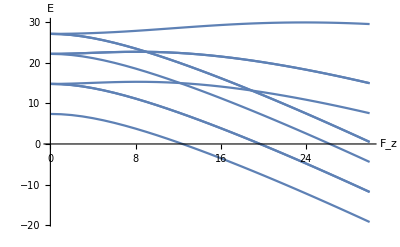

```mathematica
Show[plot1,PlotRange-> All]
```

## Figure (2)

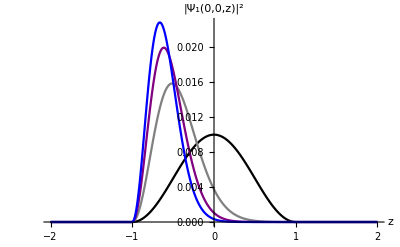

```mathematica
Show[plot2,PlotRange->All]
```

## Figure (3)

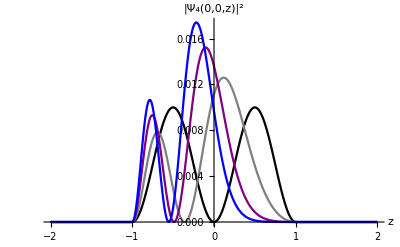

```mathematica
Show[plot3,PlotRange->All]
```

## Fig 4,5,6

## Solving Eigensystem

```mathematica
ClearAll["Global`*"]
states={{1,1,1},{2,1,1},{1,2,1},{1,1,2},{2,2,1},{2,1,2},{1,2,2},{3,1,1},{1,3,1},{1,1,3}};
statesx=Table[states⟦i,1⟧,{i,1,Length[states]}];
statesy=Table[states⟦i,2⟧,{i,1,Length[states]}];
statesz=Table[states⟦i,3⟧,{i,1,Length[states]}];

x0=-2;xf=2;dx=0.01;
x=Range[x0,xf,dx];lx=Length[x];i0=lx/2+.5;
vx=vy=vz=ConstantArray[1000000.,lx];
f=Range[0,30,1];
ns=10;
elist=ConstantArray[0*f,ns];
ψx=0*f;
ψy=0*f;

Do[
Do[If[-1<x⟦i⟧<1,vz⟦i⟧=√(2/3)f⟦k⟧*x⟦i⟧],{i,0,lx}];
Do[If[-1<x⟦i⟧<1,vy⟦i⟧=√(1/3)f⟦k⟧*x⟦i⟧],{i,0,lx}];
Do[If[-1<x⟦i⟧<1,vx⟦i⟧=0],{i,0,lx}];
(*Construct Hamiltonian*)
Hx=Hy=Hz=ConstantArray[0*x,lx];

(*Construct Hx*)
Hx⟦1,{1,2}⟧={2/dx^2+2vx⟦1⟧,-1/dx^2};
Hx⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vx⟦lx⟧};
Do[Hx⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vx⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hy*)
Hy⟦1,{1,2}⟧={2/dx^2+2vy⟦1⟧,-1/dx^2};
Hy⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vy⟦lx⟧};
Do[Hy⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vy⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hz*)
Hz⟦1,{1,2}⟧={2/dx^2+2vz⟦1⟧,-1/dx^2};
Hz⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vz⟦lx⟧};
Do[Hz⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vz⟦i⟧,-1},{i,2,lx-1}];

(*Extract normalized (112) state*)
ϕx=Chop[Eigenvectors[Hx]⟦-1⟧];
X=ϕx/(√(dx ϕx.ϕx));
If[k>21,ϕy=Chop[Eigenvectors[Hz]⟦-2⟧],ϕy=Chop[Eigenvectors[Hz]⟦-1⟧]];
Y=ϕy/(√(dx ϕy.ϕy));
If[k>21,ϕz=Chop[Eigenvectors[Hz]⟦-1⟧],ϕz=Chop[Eigenvectors[Hz]⟦-2⟧]];
Z=ϕz/(√(dx ϕz.ϕz));
(*Saving Energies and plot functions*)

elist⟦All,k⟧= Sort[Eigenvalues[Hx]]⟦statesx⟧+Sort[Eigenvalues[Hy]]⟦statesy⟧+Sort[Eigenvalues[Hz]]⟦statesz⟧;
ψx⟦k⟧=X*Y⟦i0⟧*Z⟦i0⟧;
ψy⟦k⟧=Y*X⟦i0⟧*Z⟦i0⟧;
,{k,1,Length[f]}]
```

## Creating Plots

```mathematica
color = {Black,Gray,Purple,Blue};
p = {1,11,21,31};
plot1=ConstantArray[0,5];
plot2 =plot3= 0*p;

Do[plot1⟦i⟧ = ListLinePlot[Table[{f⟦j⟧,elist⟦i,j⟧},{j,1,Length[f]}],AxesLabel->{"F_z","E"}];
,{i,1,5}]

Do[
plot2⟦i⟧=ListLinePlot[Table[{x⟦j⟧,ψx⟦p⟦i⟧,j⟧^2},{j,1,Length[x]}],PlotRange->All,PlotStyle->color⟦i⟧,AxesLabel->{"x","|Ψ_4(x,0,0)|^2"}];
plot3⟦i⟧=ListLinePlot[Table[{x⟦j⟧,ψy⟦p⟦i⟧,j⟧^2},{j,1,Length[x]}],PlotRange->All,PlotStyle->color⟦i⟧,AxesLabel->{"y","|Ψ_4(0,y,0)|^2"}]
,{i,1,Length[p]}]
```

## Figure (4)

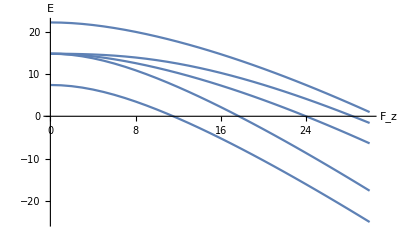

```mathematica
Show[plot1,PlotRange-> All]
```

## Figure (5)

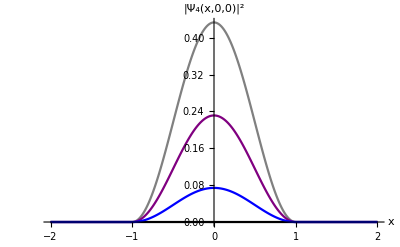

```mathematica
Show[plot2,PlotRange-> All]
```

## Figure (6)

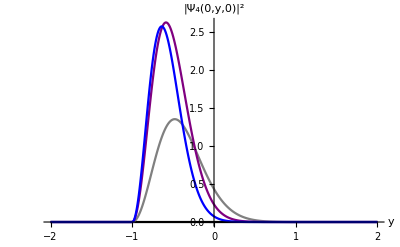

```mathematica
Show[plot3,PlotRange-> All]
```

## Absorption Figure

```mathematica
ClearAll["Global`*"]
Lorentzian[x_]:=(0.01/π)/(x^2+(0.01)^2)
states={{1,1,1},{2,1,1},{1,2,1},{1,1,2},{2,2,1},{2,1,2},{1,2,2},{3,1,1},{1,3,1},{1,1,3}};
statesx=Table[states⟦i,1⟧,{i,1,Length[states]}];
statesy=Table[states⟦i,2⟧,{i,1,Length[states]}];
statesz=Table[states⟦i,3⟧,{i,1,Length[states]}];

x0=-2;xf=2;dx=0.01;
x=Range[x0,xf,dx];lx=Length[x];i0=lx/2+.5;
vx=vy=vz=ConstantArray[1000000.,lx];
f={0,25};
elist=ConstantArray[0*f,10];
ψx=ψy=0*f;

Do[
Do[If[-1<x⟦i⟧<1,vz⟦i⟧=f⟦k⟧*x⟦i⟧],{i,0,lx}];
Do[If[-1<x⟦i⟧<1,vy⟦i⟧=0],{i,0,lx}];
Do[If[-1<x⟦i⟧<1,vx⟦i⟧=0],{i,0,lx}];

(*Construct Hamiltonian*)
Hx=Hy=Hz=ddx=ConstantArray[0*x,lx];

(*Construct Hx*)
Hx⟦1,{1,2}⟧={2/dx^2+2vx⟦1⟧,-1/dx^2};
Hx⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vx⟦lx⟧};
Do[Hx⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vx⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hy*)
Hy⟦1,{1,2}⟧={2/dx^2+2vy⟦1⟧,-1/dx^2};
Hy⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vy⟦lx⟧};
Do[Hy⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vy⟦i⟧,-1},{i,2,lx-1}];

(*Construct Hz*)
Hz⟦1,{1,2}⟧={2/dx^2+2vz⟦1⟧,-1/dx^2};
Hz⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vz⟦lx⟧};
Do[Hz⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vz⟦i⟧,-1},{i,2,lx-1}];
elist⟦All,k⟧= Sort[Eigenvalues[Hx]]⟦statesx⟧+Sort[Eigenvalues[Hy]]⟦statesy⟧+Sort[Eigenvalues[Hz]]⟦statesz⟧;
,{k,1,Length[f]}]

ddx⟦1,2⟧ = 1;ddx⟦-1,-2⟧= -1;
Do[ddx⟦i,{i-1,i+1}⟧ = {-1,1},{i,2,lx-1}];
ddx=ddx/(2dx);
(*Saving the first 3 eigenfunctions*)
X=Chop[Eigenvectors[Hx]]⟦{-1,-2,-3}⟧;
Do[X⟦i⟧=X⟦i⟧/(√(dx X⟦i⟧.X⟦i⟧)),{i,1,3}]
Y=Chop[Eigenvectors[Hy]]⟦{-1,-2,-3}⟧;
Do[Y⟦i⟧=Y⟦i⟧/(√(dx Y⟦i⟧.Y⟦i⟧)),{i,1,3}]
Z=Chop[Eigenvectors[Hz]]⟦{-1,-2,-3}⟧;
Do[Z⟦i⟧=Z⟦i⟧/(√(dx Z⟦i⟧.Z⟦i⟧)),{i,1,3}]
```

## Constructing Figure 7

```mathematica
eoptical = Range[3,50,0.1];
α1x=α1z=α1xz=α20=α225=0*eoptical;
Do[α1x⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])(Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)^2(Z⟦statesz⟦i⟧⟧.Z⟦statesz⟦j⟧⟧)^2(X⟦statesx⟦i⟧⟧.ddx.X⟦statesx⟦j⟧⟧)^2 Lorentzian[elist⟦j,2⟧-elist⟦i,2⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}];

α1z⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])(Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)^2(Z⟦statesz⟦i⟧⟧.ddx.Z⟦statesz⟦j⟧⟧)^2(X⟦statesx⟦i⟧⟧.X⟦statesx⟦j⟧⟧)^2 Lorentzian[elist⟦j,2⟧-elist⟦i,2⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}];

α1xz⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])((Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.ddx.X⟦statesx⟦j⟧⟧)+(Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.ddx.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.X⟦statesx⟦j⟧⟧) )^2 Lorentzian[elist⟦j,2⟧-elist⟦i,2⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}]

,{l,1,Length[eoptical]}]
plot3={0,0,0};
plot3⟦1⟧=ListLogPlot[Table[{eoptical⟦i⟧,α1x⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Black,AxesLabel->{"E_optical","Log[α(ω)]"}];
plot3⟦2⟧=ListLogPlot[Table[{eoptical⟦i⟧,α1z⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Gray,AxesLabel->{"E_optical","Log[α(ω)]"}];
plot3⟦3⟧=ListLogPlot[Table[{eoptical⟦i⟧,α1xz⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Purple,AxesLabel->{"E_optical","Log[α(ω)]"}];
```

## Figure 7

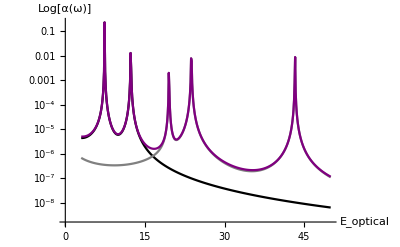

```mathematica
Show[plot3]
```

## Constructing Figure 8 and 11

```mathematica
eoptical = Range[3,50,0.1];
α20=α225=α11=0*eoptical;
Do[
α20⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])((Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(X⟦statesz⟦i⟧⟧.X⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.ddx.X⟦statesx⟦j⟧⟧)+(Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(X⟦statesz⟦i⟧⟧.ddx.X⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.X⟦statesx⟦j⟧⟧) )^2 Lorentzian[elist⟦j,1⟧-elist⟦i,1⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}];

α225⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])((Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.ddx.X⟦statesx⟦j⟧⟧)+(Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.ddx.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.X⟦statesx⟦j⟧⟧) )^2 Lorentzian[elist⟦j,2⟧-elist⟦i,2⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}];

α11⟦l⟧= (10^-10 dx^2)/eoptical⟦l⟧Sum[(1-KroneckerDelta[i,j])((Y⟦statesy⟦i⟧⟧.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.ddx.X⟦statesx⟦j⟧⟧)+(Y⟦statesy⟦i⟧⟧.ddx.Y⟦statesy⟦j⟧⟧)(Z⟦statesz⟦i⟧⟧.Z⟦statesz⟦j⟧⟧)(X⟦statesx⟦i⟧⟧.X⟦statesx⟦j⟧⟧) )^2 Lorentzian[elist⟦j,2⟧-elist⟦i,2⟧- eoptical⟦l⟧] ,{i,1,Length[states]},{j,1,Length[states]}]

,{l,1,Length[eoptical]}]

plot4={0,0};
plot4⟦1⟧=ListLogPlot[Table[{eoptical⟦i⟧,α20⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Black,AxesLabel->{"E_optical","Log[α(ω)]"}];
plot4⟦2⟧=ListLogPlot[Table[{eoptical⟦i⟧,α225⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Purple,AxesLabel->{"E_optical","Log[α(ω)]"}];
plot5 = ListLogPlot[Table[{eoptical⟦i⟧,α11⟦i⟧},{i,1,Length[eoptical]}],Joined->True,PlotStyle->Purple,AxesLabel->{"E_optical","Log[α(ω)]"}];
```

## Figure 8

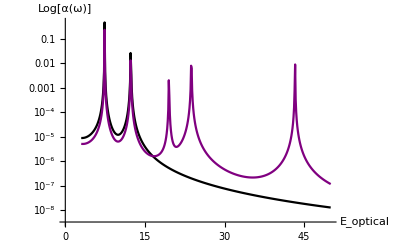

```mathematica
Show[plot4]
```

## Figure 11 (numerical)

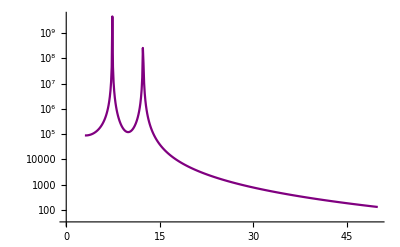

```mathematica
Show[plot5]
```

## Comparing Exact and Numerical values

```mathematica
f=Range[0,30];
eexact={ConstantArray[0,31],ConstantArray[0,31]};
exactstates={1,10};color={Black,Purple};
plotnum=plotex={0,0};
Do[
eexact⟦j,i⟧=e/.FindRoot[AiryAi[(2*f⟦i⟧)^(1/3) (-0.5 e/f⟦i⟧+1)] AiryBi[(2*f⟦i⟧)^(1/3)(-0.5 e/f⟦i⟧-1)]-AiryAi[(2*f⟦i⟧)^(1/3) (-0.5 e/f⟦i⟧-1)] AiryBi[(2*f⟦i⟧)^(1/3) (-0.5 e/f⟦i⟧+1)],{e,ez⟦exactstates⟦j⟧,f⟦i⟧⟧}];
plotnum⟦j⟧ = ListPlot[Table[{f⟦k⟧,ez⟦exactstates⟦j⟧,k⟧},{k,2,Length[f]}],PlotStyle->Purple];
plotex⟦j⟧=ListLinePlot[Table[{f⟦k⟧,eexact⟦j,k⟧},{k,2,Length[f]}],PlotStyle->Black];
,{i,2,Length[f]},{j,1,2}]
```

## Figure 9

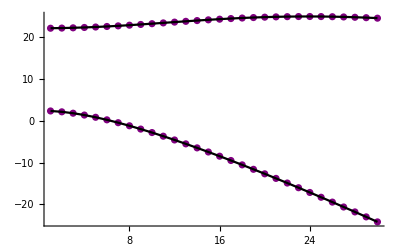

```mathematica
Show[plotnum,plotex,PlotRange->All]
```

```mathematica
ClearAll["Global`*"]

x0=-2;xf=2;dx=0.01;
x=Range[x0,xf,dx];lx=Length[x];
vx=vy=vz=ConstantArray[1000000.,lx];
f=30;
elist=ez=ConstantArray[0*f,10];

Do[If[-1<x⟦i⟧<1,vz⟦i⟧=f*x⟦i⟧],{i,0,lx}];
(*Construct Hamiltonian*)
Hz=ConstantArray[0*x,lx];
(*Construct Hz*)
Hz⟦1,{1,2}⟧={2/dx^2+2vz⟦1⟧,-1/dx^2};
Hz⟦lx,{lx-1,lx}⟧ = {-1/dx^2,2/dx^2+2vz⟦lx⟧};
Do[Hz⟦i,{i-1,i,i+1}⟧=1/dx^2{-1,2+2 dx^2 vz⟦i⟧,-1},{i,2,lx-1}];

e=Sort[Eigenvalues[Hz]]⟦4⟧;
ψz4=Eigenvectors[Hz]⟦-4⟧;
ψz4=ψz4/(√(dx ψz4.ψz4));
f=30;
cod=(-AiryBi[(2f)^(1/3)(-0.5*e/f+1)])/AiryAi[(2f)^(1/3)(-0.5*e/f+1)];
ψzex[z_]:=(cod AiryAi[(2f)^(1/3)(-0.5*e/f+z)]+AiryBi[(2f)^(1/3)(-0.5*e/f+z)])/(√NIntegrate[(cod AiryAi[(2f)^(1/3)(-0.5*e/f+x)]+AiryBi[(2f)^(1/3)(-0.5*e/f+x)])^2,{x,-1,1}]);
plot5={0,0};
plot5⟦1⟧=ListPlot[Table[{x⟦i⟧,ψz4⟦i⟧^2},{i,1,Length[x]}],PlotStyle->Purple,AxesLabel->{"z","ψz_(l = 4)(z)"}];
plot5⟦2⟧=Plot[ψzex[x]^2,{x,-1,1},PlotStyle->Black];
```

## Figure 10

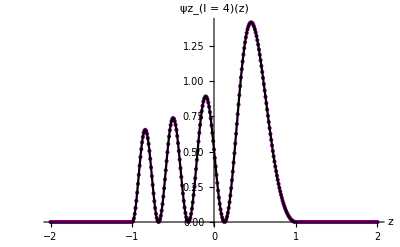

```mathematica
Show[plot5]
```